## Periodic solutions, limit cycles, and the Poincaré map

### The Poincaré return map

#### The First-Return Map Φ

Consider a two-dimensional system whose phase curves wind around an equilibrium position in the phase plane, which we will call the “center”.  The curves might spiral in closer to the center, spiral out away from the center, or perhaps even close on themselves.

Draw a ray from the center in any direction whatsoever.  (It is often convenient to make it  horizontal or vertical.)  Let A>0 be a coordinate on the ray denoting the distance from the center.  The a phase curve starting at A will wind around the center a return to a position at a distance Φ(A) from the center (the first time it returns to the ray).  This defines the function Φ, called the Poincaré map and the ray is called a Poincaré section.

```mathematica
polarToCartestian={r->√(x^2+y^2),θ->ArcTan[x,y]};baseDE=Simplify@Expand[{Dt[x],Dt[y]}/.First@Solve[{Dt[r]==2r(1-r)(r-0.24)(r-0.74),Dt[θ]==1}/.polarToCartestian,{Dt[x],Dt[y]}]];

(* differential equations/Poincare code *)
Clear[baseSol];
baseSol[b_?NumericQ]:=baseSol[b]= (* baseSol *)
NDSolveValue[{
{x'[t],y'[t]}==(baseDE/.{x->x[t],y->y[t]}), (*  baseDE *)
x[0]==0,y[0]==b,
WhenEvent[x[t]==0&&y[t]>0,"StopIntegration"]},
{x,y},{t,0,Infinity}];

baseFlow=StreamPlot[baseDE,{x,-1.1,1.1},{y,-1.1,1.1},StreamStyle->{Gray,Opacity[0.5]}];

basePlot=ParametricPlot[
Evaluate@Table[
Through[baseSol[b][t]],{b,0.1,0.9,0.2}],
{t,0,2Pi},PlotStyle->Table[Directive[Thick,ColorData["DarkRainbow"][b]],{b,0.1,0.9,0.2}],
Epilog->{Thick,HalfLine[{{0,0},{0,1}}],PointSize[Medium],Point[{0,0}],
Table[
{Text[Subscript[A,Round[(b+0.1)/0.2]],Through[baseSol[b][0]],{-1.5,0}],
Text[Φ[Subscript[A,Round[(b+0.1)/0.2]]],Through[baseSol[b][2Pi]],{1.25,0}]},
{b,0.1,0.9,0.2}]},
Ticks->None
]/.Line->Arrow;

Show[basePlot,baseFlow]
```

-Graphics-

Figure FigureNumbered.  Phase portrait showing the Poincaré map (first-return map) Φ.

Another way to present the Poincaré map is in a traditional graph plotting (A,Φ=Φ(A)).  Note that when a trajectory closes on itself, Φ(A)=A.  It is natural then to compare the graph of Φ(A) with the line Φ=A.

#### The Lamerey staircase

The Poincaré map Φ(A) gives the position of the first time the system returns to the Poincaré section having started at position A.  The second time, the system will be at position Φ(Φ(A))≡Φ^2(A), the third time at Φ(Φ(Φ(A)))≡Φ^3(A), etc.  The dynamics of this scheme can be viewed on the plot of the Poincaré map and the diagonal line Φ=A.  Each input A=A_1, generates value via Φ(A_1), which becomes new input A=A_2≡Φ(A_1). This can be viewed as step, that goes from the “input” line Φ=A at the point (A_1,A_1), to the Poincaré map at (A_1,A_2=Φ(A_1)), and back to the input line at (A_2,A_2).  A sequence of steps plotted on the Poincaré graph looks like a staircase, called the Lamerey staircase:

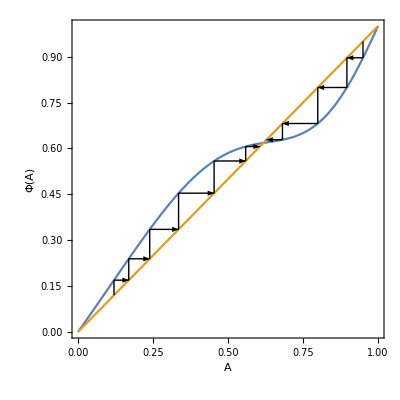

```mathematica
PacletInstall["http://www.wolframcloud.com/obj/mroge02/math212/diffEqClass.paclet",IgnoreVersion->True];
Needs@"diffEqClass`";
(*lamereyStairs[f_,a0_,n_]:=Module[{h=Arrow},
(h=h/.{Arrow->Line,Line->Arrow})[#]&/@
Partition[
Transpose[{Most[#],Rest[#]}]&@Riffle[#,#]&@NestList[f,a0,n],
2,1]
];*)

With[{f=#+0.12Sin[Pi(#+#^2)]&,n=5},
Plot[{f[a],a},{a,0,1},Epilog->{Arrowheads[{0,0,0,0.03,0}],lamereyStairs[f,0.12,6],lamereyStairs[f,0.95,4]},
AspectRatio->1,Frame->True,FrameTicks->None,PlotRangePadding->0,FrameLabel->{A,Φ[A]}]]
```

Figure FigureNumbered.  Phase portrait showing the Lamerey staircase near a stable cycle.

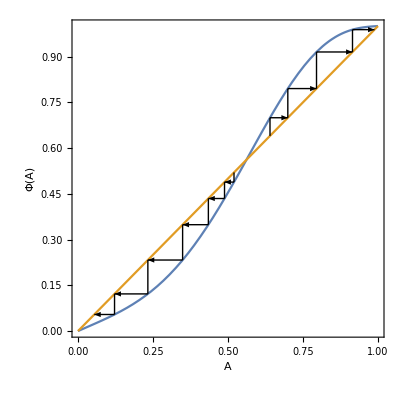

```mathematica
With[{f=#-0.12Sin[Pi(1.5#+0.5#^2)]&,n=5},
Plot[{f[a],a},{a,0,1},Epilog->{Arrowheads[{0,0,0,0,0,0.03,0}],lamereyStairs[f,0.52,6],lamereyStairs[f,0.64,4]},
AspectRatio->Automatic,Frame->True,FrameTicks->None,PlotRangePadding->0,FrameLabel->{A,Φ[A]}]]
```

Figure FigureNumbered.  Phase portrait showing the Lamerey staircase near an unstable cycle.

#### Limit cycles and stability

In the Lamerey figures FigureNumbered and FigureNumbered, where the Poincaré map Φ(A) crosses the line Φ=A corresponds to a limit cycle.  In Figure FigureNumbered, each trajectory that starts near the limit cycle returns to the Poincaré section closer to the equilibrium.  This is a stable limit cycle.  In Figure FigureNumbered, each trajectory that starts near the limit cycle returns to the Poincaré section further from the equilibrium.  This is a unstable limit cycle.

We can deduce the type of stability of a limit cycle from the derivative Φ'(A) of the Poincaré map, when it is different from 1:
	If Φ'(A)<1, the cycle is stable.
	If Φ'(A)>1, the cycle is unstable.

#### Perturbation

A perturbation of a system

ẋ=  f(x,y)
ẏ=g(x,y)

has the form

ẋ=  f(x,y)+ε ξ(x,y)
ẏ=g(x,y)+ε η(x,y)

where ε is a real parameter and ξ(x,y) and η(x,y) are arbitrary smooth functions.  As ε⟶0, the system (EquationNumbered) approaches (EquationNumbered).

#### Closed phase curves

We saw earlier that the Lotka-Volterra system,

ẋ=  κ x-α xy
ẏ=-λ y+β xy

seemed to have cycles, i.e., closed phase curves ("click for figure"),  but it was impossible to tell whether they returned precisely their initial points.

As we have seen, this sort of autonomous system is equivalent to non-autonomous separable differential equation:

dy/dx=(y(βx-λ))/(x(κ-α y))=(y/(κ-α y))/(x/(βx-λ)).

This in turn can be factored into a direct product system, with a new time variable, say s, whose phase curves coincide the phase/integral curves of equations (EquationNumbered) and (EquationNumbered).

dx/ds=x/(βx-λ)
dy/ds=y/(κ-α y)

Solving (EquationNumbered), we get

∫(βx-λ)/x dx=∫(κ-α y)/y dy+C,

or

f(x)+g(y)=C, with f(x)=βx-λ log x, g(y)=αy-κ log y.

The graphs of f and g are concave up.  Therefore f+g will also be concave up (somewhat like a bowl) and the cross-sections where f+g is constant are cycles.  This means that the populations x, y of pike and carp oscillate periodically

```mathematica
Plot3D[3x-2Log[x]+3y-Log[y],{x,0,2},{y,0,1},MeshFunctions->{#3&},
MeshStyle->{Thick,RGBColor[0.880722, 0.611041, 0.142051]},PlotPoints->50,
PlotStyle->{Opacity[0.7],RGBColor[0.6842085,0.7533895,0.854899]},PlotRange->{4.5,8},BoxRatios->{2,1,1.2},Lighting->"Neutral",ClippingStyle->None,ViewPoint->{0.,0.8,5.},ViewVertical->{0,1,0}]
```

-Graphics3D-

Figure FigureNumbered.  The phase cycles as cross-sections of the potential function for the Lotka-Volterra equations.

#### Persistence of limit cycles

Suppose we are little off in our ideal equations describing the carp-pike system (in the Lotka-Volterra equations).  We have seen that slight perturbation of a system whose phase flow is a rotation results in phase curves that spiral in or spiral out from the equilibrium.  How can we tell if the cycles turn into spirals in this case?

We can consider a slight perturbation of the system (EquationNumbered)

ẋ=x ( κ -α y+ϵ f(x,y))
ẏ=y(-λ +β x+ϵ g(x,y))

It is reasonable to assume that the perturbing term, ϵ x f(x,y), is proportional to x, since if there are no carp (x=0), the rate of growth ẋ will be zero; likewise, the other term, ϵ y g(x,y),will be proportional to y.Click on the button below to explore how different perturbations change the system as ϵ varies.

```mathematica
Button["interactive example",
If[!MemberQ[$Path,NotebookDirectory[]],AppendTo[$Path, NotebookDirectory[]],$Path];
Needs["math212`"];
math212`showExample[
"ODE Portrait",
"The perturbed Lotka-Volterra system",
"Move the ϵ slider to control the magnitude of the perturbation.  Enter perturbations into the fields.",
Manipulate[
StreamPlot[{-x+3 x y+ϵ f,2 y-3 x y+ϵ g},{x,0,2},{y,0,1},AspectRatio->Automatic,ImageSize->350,
PlotLabel->"ẋ=x(κ-α y+ϵ f(x,y)),  ẏ=y(-λ+β x+ϵ g(x,y))"],
{{f,x^2+y},InputField},{{g,x+y^2},InputField},
{{ϵ,0.},-2.*^-1,2.*^-1,Appearance->"Labeled"}
],
{}
]
]
```

interactive example

Some things to observe in the interactive example:  (1) The perturbed system has an equilibrium point that varies smoothly as ϵ changes. (This can be proved with the Implicit Function Theorem of multivariable calculus.)  (2) The phase curves are not closed when ϵ≠0, so the populations of the carp and pike do not vary periodically.

It is easy to see that in this case as well any slight rotation of the phase velocity vectors produces curves that spiral in toward or out from the equilibrium point.  This turns out to be connected to the Poincaré map Φ.  Recall that a closed phase curve corresponds to Φ(A)=A and the graph of Φ crossing the diagonal line in the Lamerey diagram.  In the unperturbed Lotka-Volterra system (EquationNumbered) the Poincaré map is the identity map Φ(A)=A for all A and its graph coincides with the diagonal.  A perturbation that moves the graph even a little off the line will destroy the closed phase curves.  That is what happens in the interactive example above no matter how small ϵ≠0 is.

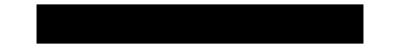

When we form another system by adding ϵ terms as in (EquationNumbered), we can think of it as a “nearby” system for ϵ in a open interval containing 0.  Suppose however a system has an isolated limit cycle.  In that case the graph of the Poincaré map crosses the diagonal.  If a perturbation moves the graph only slightly, it will still cross and the perturbed system will have a limit cycle nearby the original limit cycle.   As ϵ varies, let the Poincaré map of the perturbed system be Φ(A,ϵ).  Then studying the behavior of a cycle is equivalent to studying the behavior of the equation Φ(A,ϵ)-A=0 as ϵ varies.  The implicit function theorem can be used to show that the root A_ϵ varies smoothly with ϵ.  It requires that the derivative of the left-hand side of the equation is nonzero.  In other words, if at a cycle passing through A (so that Φ(A)=A)

Φ'(A)≠1,

then the graph crosses the diagonal.  Such a cycle is called nondegenerate.  Consequently:

Theorem.  If a system has a nondegenerate limit cycle, every nearby system also has a limit cycle.

The figures below illustrate such a system and its Poincaré map.

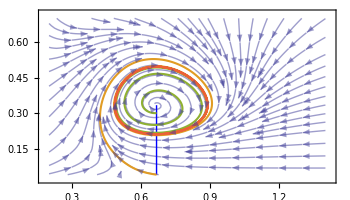

```mathematica
With[{exact=(-5.+3 x+3 y-2Log[x]-Log[y])},With[{ϵ=2,f=(2-3 x )exact,g=-(-1+3 y)exact},
Show[
StreamPlot[{-x+3 x y+ϵ x f, 2y-3 x y+ϵ y g},{x,0.2,1.4},{y,0.04,0.7},StreamStyle->Opacity[0.5],AspectRatio->Automatic,ImageSize->350],
(*ContourPlot[exact==0,{x,0.3,1.4},{y,0.02,0.7}],*)
Graphics[{Blue,Thick,Line[{{2/3,1/3},{2/3,0.04}}]}],
With[{sol=ParametricNDSolveValue[{{x'[t],y'[t]}==({-x+3 x y+ϵ x f,2y-3 x y+ϵ y g}/.{x->x[t],y->y[t]}),x[0]==2/3,y[0]==b},{x[t],y[t]},{t,0,17.8},{b}]},
ParametricPlot[Evaluate[Table[sol[b],{b,{1/3,0.04,0.3,-1/3 ProductLog[0,-27/(4 ⅇ^3)]}}]],{t,0,17.8}]
]
]
]]
```

Figure FigureNumbered.  Phase flow with a limit cycle, showing the Poincaré map (first-return map).

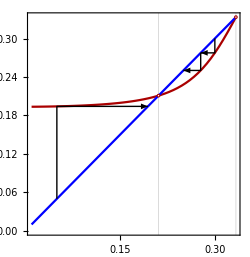

```mathematica
With[{exact=(-5.+3 x+3 y-2Log[x]-Log[y])},With[{ϵ=1,f=(2-3 x )exact,g=-(-1+3 y)exact},
With[{sol=ParametricNDSolveValue[{{x'[t],y'[t]}==({-x+3 x y+ϵ x f,2y-3 x y+ϵ y g}/.{x->x[t],y->y[t]}),x[0]==2/3,y[0]==b,WhenEvent[x[t]<2/3,Sow[y[t]];"StopIntegration"]},{x[t],y[t]},{t,0,30},{b},Method->{"ParametricCaching"->None}]},
With[{poincareMap=Interpolation[Table[{bb,Reap[sol[bb]][[-1,1,1]]},{bb,0.01,1/3.,0.01}]~Append~{1/3.,1/3.}]},
Plot[{poincareMap[y],y},{y,0.01,1/3},PlotStyle->{Darker@Red,Blue},Frame->True,AspectRatio->Automatic,
Epilog->{EdgeForm@Directive[Thickness[Medium],Darker@Red],White,Disk[N@{-1/3 ProductLog[-27/(4 ⅇ^3)],-1/3 ProductLog[-27/(4 ⅇ^3)]},0.002],Disk[N@{1/3,1/3},0.002],Black,Arrowheads[0.04],Arrow[{{#,#},{#,poincareMap[#]},{poincareMap[#],poincareMap[#]}}]&/@{0.05,0.3,poincareMap[0.3]}},
GridLines->{{-1/3. ProductLog[-27/(4 ⅇ^3)],1/3.},{}},
ImageSize->250]
]]]]
```

Figure FigureNumbered.  The Lamerey diagram for the limit cycle system.  The Poincaré map (red) crosses the diagonal (blue).

Figure (FigureNumbered) below depicts three systems that are near each other.  The first one has two nondegenerate cycles, which coalesce into a degenerate one as the parameter changes.  As the parameter continues to change, the cycle disappears.  The value of parameter at which there is a degenerate cycle is therefore a critical point that separates there being no cycles from there being two.  Such a point is called a bifurcation point.

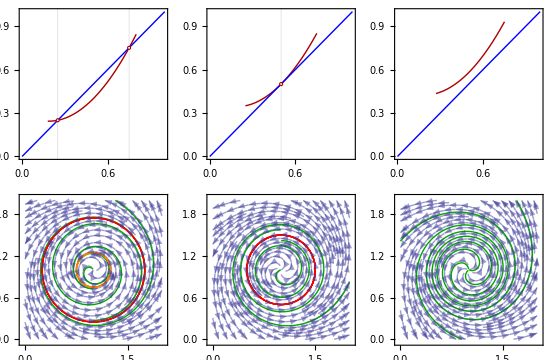

```mathematica
GraphicsGrid[{{
With[{sols=A/.Solve[A+1.6(A-0.5)^2-0.1==A(*//Rationalize*),A]},Plot[{If[0.18<A<0.8,A+1.6(A-0.5)^2-0.1],A},{A,0,1},PlotStyle->{Darker@Red,Blue},Frame->True,AspectRatio->Automatic,
Epilog->{EdgeForm@Directive[Thickness[Medium],Darker@Red],White,Disk[{#,#},Scaled[0.01]]&/@sols(*,Disk[N@{1/3,1/3},0.002]*)},
GridLines->{sols,{}}]
],
With[{sols={0.5}},
Plot[{If[0.25<A<0.75,A+1.6(A-0.5)^2],A},{A,0,1},PlotStyle->{Darker@Red,Blue},Frame->True,AspectRatio->Automatic,
Epilog->{EdgeForm@Directive[Thickness[Medium],Darker@Red],White,Disk[{#,#},Scaled[0.01]]&/@sols(*,Disk[N@{1/3,1/3},0.002]*)},
GridLines->{sols,{}}]
],
Plot[{If[0.27<A<0.75,A+1.6(A-0.5)^2+0.08],A},{A,0,1},PlotStyle->{Darker@Red,Blue},Frame->True,AspectRatio->Automatic]
},{With[{de={Dt[x],Dt[y]}/.First@Solve[{Dt[r]==(r-1/4)(r-3/4)/.{r->√((x-1)^2+(y-1)^2)},Dt[θ]==1/.θ->ArcTan[(x-1),(y-1)]},{Dt[x],Dt[y]}]//Together//Simplify},
Show[
StreamPlot[de,{x,0,2},{y,0,2},StreamStyle->Opacity[0.5]],
With[{sol=ParametricNDSolveValue[{{x'[t],y'[t]}==(de/.{x->x[t],y->y[t]}),x[0]==1,y[0]==b,
WhenEvent[Abs[x[t]-1]>1||Abs[y[t]-1]>1||Norm[{x[t]-1,y[t]-1}]<0.01,"StopIntegration"]},{x[t],y[t]},{t,-2Pi,2Pi},{b}]},
Table[With[{p=sol[b]},ParametricPlot[p,Evaluate[{t}~Join~First@First[p/.t->"Domain"]],PlotStyle->(b/.Thread[{1/4,3/4,0.2,0.5,0.8}->{Directive[Thick,Red],Directive[Thick,Orange],Darker@Green,Darker@Green,Darker@Green}])]],{b,{0.2,0.5,0.8,1/4,3/4}}]
]
]
],
With[(*middle*){de={Dt[x],Dt[y]}/.First@Solve[{Dt[r]==(r-1/2)(r-1/2)/.{r->√((x-1)^2+(y-1)^2)},Dt[θ]==1/.θ->ArcTan[(x-1),(y-1)]},{Dt[x],Dt[y]}]//Together//Simplify},
Show[
StreamPlot[de,{x,0,2},{y,0,2},StreamStyle->Opacity[0.5]],
With[{sol=ParametricNDSolveValue[{{x'[t],y'[t]}==(de/.{x->x[t],y->y[t]}),x[0]==1,y[0]==b,
WhenEvent[Abs[x[t]-1]>1||Abs[y[t]-1]>1||Norm[{x[t]-1,y[t]-1}]<0.01,"StopIntegration"]},{x[t],y[t]},{t,-3Pi,3Pi},{b}]},
Table[With[{p=sol[b]},ParametricPlot[p,Evaluate[{t}~Join~First@First[p/.t->"Domain"]],PlotStyle->(b/.Thread[{1/2,0.2,0.8}->{Directive[Thick,Red],Darker@Green,Darker@Green}])]],{b,{0.2,0.8,1/2}}]
]
]
],
With[(*last*){de={Dt[x],Dt[y]}/.First@Solve[{Dt[r]==((r-1/2)^2+1/30)/.{r->√((x-1)^2+(y-1)^2)},Dt[θ]==1/.θ->ArcTan[(x-1),(y-1)]},{Dt[x],Dt[y]}]//Together//Simplify},
Show[
StreamPlot[de,{x,0,2},{y,0,2},StreamStyle->Opacity[0.5]],
With[{sol=ParametricNDSolveValue[{{x'[t],y'[t]}==(de/.{x->x[t],y->y[t]}),x[0]==1+Cos[b]/2,y[0]==1+Sin[b]/2,
WhenEvent[Abs[x[t]-1]>1||Abs[y[t]-1]>1||Norm[{x[t]-1,y[t]-1}]<0.01,"StopIntegration"]},{x[t],y[t]},{t,-3Pi,3Pi},{b}]},
Table[With[{p=sol[b]},ParametricPlot[p,Evaluate[{t}~Join~First@First[p/.t->"Domain"]],PlotStyle->Darker@Green]],{b,{0,2Pi/3,4Pi/3}}]
]
]
]}},ImageSize->550]
```

Figure FigureNumbered.  Three systems: Lamerey diagrams and phase spaces.  The limits cycles on the left coalesce into a degenerate cycle, which disappears in the system on the right.

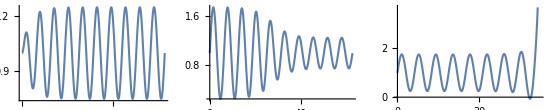

```mathematica
With[{de={Dt[x],Dt[y]}/.First@Solve[{Dt[r]==1/2
(r-1/4)(r-3/4)/.{r->√((x-1)^2+(y-1)^2)},Dt[θ]==1/.θ->ArcTan[(x-1),(y-1)]},{Dt[x],Dt[y]}]//Simplify},
With[{sol=ParametricNDSolveValue[{{x'[t],y'[t]}==(de/.{x->x[t],y->y[t]}),x[0]==1,y[0]==b},{x[t],y[t]},{t,0,20Pi},{b}]},
GraphicsRow[
Table[With[{p=Quiet@sol[b]},Plot[First@p,Evaluate[{t}~Join~First@First[p/.t->"Domain"]],PlotStyle->(b/.Thread[{0.2,0.5,0.8}->{Darker@Green,Darker@Green,Darker@Green}])]],{b,Reverse@{0.249999,0.2505,0.9999999}}],
ImageSize->550]
]]
```

Figure FigureNumbered.  The solutions x(t) to the first system with an initial condition in each of the three regions into which the two limit cycles divide the plane.  The shift in the amplitude illustrates the transition of the phase curve from or to a limit cycle; the one on the right, if continued, has an amplitude that approaches infinity.

The study of the appearance and splitting of phenomena such as cycles is called bifurcation theory.  It has applications to the study of sudden changes in the qualitative behavior of systems under a smooth change of a parameter in a variety of sciences, economics, and mechanical and electrical engineering.  It is sometimes called catastrophe theory.

Looking at Figure (FigureNumbered) we can see that the distance between the cycles diminishes rough as the roots of a parabola as the parabola rises steadily above the xaxis (consider the approximation by power series up to terms of degree two).  Thus the velocity at which the cycles approach each other approaches infinity as the system approaches the middle one with a degenerate cycle.  This explains why it is difficult to stop a catastrophe after its imminence has become noticeable.  [V.I. Arnold, Ordinary Differential Equations, Springer-Verlag 1992, p. 46].

Exercise

Discuss the bifurcation of cycles as the parameter c changes in the system given in polar coordinates by

ṙ | = | cr-r^3+r^5
θ̇ | = | 1

(Discuss the stability of the cycles and how they coalesce or separate.)

Show that around ε=0 , there is a single limit cycle, which is nondegenerate according the definition above:

ṙ | = | (1+ε)r-3 r^2+3 r^3-r^4
θ̇ | = | 1

However, show that the sensitivity of the radius of the cycle as  given by dr/dεapproaches infinity as ε⟶0 .(Note that r-3 r^2+3 r^3-r^4=(r(1-r))^3 .)

Show that around ε=0, the cycle is degenerate:

ṙ | = | (1+ε)r-(3+ε)r^2+r^3-r^4
θ̇ | = | 1

Comparing with exercise HomeworkTextNumbered, conclude that one cannot reliably assess the nondegeneracy of a limit cycle by perturbing just one coefficient of a differential equation.  Indeed, generally one needs to perturb all coefficients independently and simultaneously.

### Linearization about a cycle

#### Symmetries of the solution space of a homogeneous linear ODE

We recall some facts about first-order linear ODEs we treated earlier.  The homogeneous equation

(d y)/(d x)+P(x) y=0

is separable and for an initial condition (x_0,y_0) has a solution given by

y(x)=y_0 e^(-∫_x_0^x P(t) ⅆt).

When y_0=0, the solution (EquationNumbered) is a constant zero; it is called the trivial solution. It is easy to check that the solutions form a linear space:  If y_1,y_2 are any two solutions, and k is any scalar (number), then

y_1+y_2 and k y_1

are also solutions.  In linear algebra, the solution space would be called a one-dimensional vector space.  It is called one-dimensional because all solutions may be obtained from just one nontrivial solution via the linear combinations (EquationNumbered), namely k y_1.

Since scaling a solution by a constant produces another solution, it follows that the extended phase space (x,y) is invariant under scaling of the y coordinate:  A scaling or dilation is a geometric transformation that multiplies the coordinates by a constant factor k.  Recall from elementary analytic geometry that the graph of an equation F(x,y)=0 undergoes the same transformation when y is replaced by y/k to get F(x,y/k)=0.  The same thing happens here (see Exercises below).  A dilation is a smooth transformation since the mapping (x,y)↦(x,ky) is differentiable.  Since a dilation is a smooth transformation that preserves the structure of the extended phase space (that is to say, the integral curves), it is sometimes called a diffeomorphism (diffeo- differentiable, morphe form), but we will call it simply a symmetry or sometimes a smooth symmetry.  We see that this system is invariant under a one-parameter group of symmetries, the parameter being k.  The whole solution space of the homogeneous linear equation (EquationNumbered) may be obtained from the action of the group of dilations on any nontrivial solution.  Something similar happens in higher dimensional linear systems.

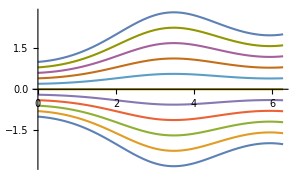

```mathematica
With[{sol=ParametricNDSolveValue[{y'[x]==(1/3+Sin[x])y[x]/3,y[0]==y0},y,{x,0,4Pi},{y0}]},
Plot[Evaluate@Table[sol[b][x],{b,-1.,1.,0.2}],{x,0,2Pi},AxesOrigin->{0,0},ImageSize->300]
]
```

Figure FigureNumbered.  The dilations of a solution of a linear differential equation.

#### Phase flow

In this section, we would like to think of x as “time” and y as “position” and discuss the evolution of the system in equation (EquationNumbered) as “time” increases.  While the example at hand is a first-order system whose phase space is a line, our remarks apply to a phase space of any dimension.  Every position y_0 in phase space corresponds to an initial condition y(0)=y_0.  The corresponding solution given by equation (EquationNumbered) may be described in terms of a function φ^x, where x is a parameter, by

y(x)=φ^x(y_0)=^def e^(-∫_x_0^x P(t) ⅆt)y_0.

Thus the function φ^x(y_0) depends on two variables, the time x and the position y_0.  The function φ^x maps each point, which is an initial condition at time 0, in phase space to the position in phase space to which the point will have moved at time x. Such a function called the phase flow of the differential equation (EquationNumbered).  The phase flow can be considered a symmetry of the phase space, in that an integral curve is mapped to itself, each point being moved to the position at which it will lie at time x.One can extend the symmetry to the phase field itself by defining the action of φ^x on the phase vectors to transport each tangent vector at each y_0 to the tangent vector at  φ^x(y_0).

Theorem.  The phase flow φ^x(y_0) of a homogeneous linear differential equation is linear in y_0.

Proof, in the case of  equation (EquationNumbered):  For a fixed x,equation (EquationNumbered) defines φ^x(y_0)=A y_0, where A is constant. ■

Theorem.  The phase flow φ^x(y_0) satisfies the group properties, φ^0(y_0)=y_0 and  φ^b(φ^a(y_0))=φ^(a+b)(y_0)

Proof:  This should seem obvious when you think about it the right way. The first property φ^0(y_0)=y_0 is part of the definition of flow.  For the second, consider this.  The position y_1=φ^a(y_0)is the position to which a particle starting at y_0 and moving under the flow of the differential equation will have moved at time a. After another time b, the particle which was at y_1 will have moved to φ^b(y_1)=φ^b(φ^a(y_0)). Since the whole time expired is a+b, this position is also φ^(a+b)(y_0). ■

Remark:  That this is true for the flow given in equation (EquationNumbered) can been shown directly from the formula.

#### Groups of symmetries

We have used symmetries before, usually in the form of substitutions.  In linear ODEs, we have used ones of the form y=y_1 u, where y_1 is a known solution, in such applications as the reduction of order and variation of parameters.

Technically, when we speak of a group of symmetries, we have in mind a certain kind of set.  For instance suppose we have a one-parameter set so that for each real number t, there belongs to the set a mapping φ^t (where t is a parameter, not a power).  Then we require that  φ^0(x)=x and φ^s(φ^t(x))=φ^(s+t)(x), the group properties.  For instance, on the set of real numbers x, the mappings φ^t(s)=e^t x for any t satisfy the requirements.  One can show that the group properties imply that φ^-t is the inverse function of φ^t.  Such set of symmetries — one for each real number t and satisfying the group properties — is called a one-parameter group of symmetries.

In differential equations, we study two fields, phase fields and direction fields (or extended phase fields).  For a field invariant under a group of symmetries φ^t, the group defines a flow on the domain of the field that carries integral curves into integral curves as discussed above.  For each point x_0, the function x(t)=φ^t(x_0) defines a flow path, sometimes called the orbit of x_0 under the action of the symmetry group.  The parameter t defines a new coordinate; in a plane, to complete the coordinate system, one needs only a transversal of the orbits, a line that crosses the orbits and is not tangent to them, which may be curved such as the unit circle in polar coordinates, which crosses the radial lines emanating from the origin.  The transversal serves as a (possibly curved) coordinate axis t=0.

The other way we use symmetries, via substitutions, is connected to flows. Substitutions transform direction fields and differential equations.  Just as a substitution u=φ(x) transforms one integral into another in single-variable calculus, a substitution (s,u)=φ(t,x) transforms a differential equation dx/dt=v(t,x) into another one du/ds=w(s,u).  Correspondingly, in geometrical terms, the direction field and the integral curves of the first equation are mapped to the direction field and the integral curves of the second.  One significant difference between the two kinds of symmetries concerns the domain and codomain.  For a symmetry they are always the same, and symmetry maps a point in an extended phase space to another point in the same extended phase space and the directions of the field are unaltered.  A substitution maps the extended phase space of one differential equation to a different extended phase space of another differential equation.

These two ways are connected as follows.  Substitutions usually aid in solving a differential equation by transforming a differential equation into an equation with a group of symmetries.  In particular, when a direction field is invariant under translations along a coordinate axis, then that coordinate can be integrated (see examples below).  Conversely, when the direction field is invariant, one can find a substitution that transforms the direction field into one that is invariant under translations.  This comes from the group properties.  It makes the translation φ^s:t↦s+t correspond to the symmetry of the direction field.

This property of being able to construct an integrable dimension is one of the deeper results of differential equations: if a field is invariant under the action of a one-parameter group of symmetries, the problem of finding the integral curves of the field may be reduced to finding the integral curves of a field with one dimension less via a suitable choice of local coordinates, i.e., a suitable substitution.  In the case of a first-order equation, the substitution transforms the equation into one that may be solved by separation of variables.  Thus the problem of finding the integral curves of the two-dimension direction field is reduced to two one-dimensional problems, namely, two integrals, one with respect to each variable.

#### Linearization

Linear equations are important in part because smooth functions are approximated well in a neighborhood by their linear Taylor polynomials,

P(x)≈P(x_0)+P'(x_0)(x-x_0),

or more generally,

f(x,y)≈f(x_0,y_0)+(∂f)/(∂x)(x_0,y_0)(x-x_0)+(∂f)/(∂y)(x_0,y_0)(y-y_0).

Replacing functions in a system by their linear Taylor polynomials is called linearization of the system.

For instance, at an equilibrium point (x_0,y_0) of the system

{ẋ | = | f(x)
ẏ | = | g(y)

we have f(x_0)=g(y_0)=0. The linearization of this system leads to a system of a form we have seen,

{Ẋ | = | a X
Ẏ | = | b Y

where X=x-x_0, Y=y-y_0 are local variables and a=f'(x_0), b=g'(y_0) are the differential coefficients.  It is a local approximation, local in the sense that there is an open neighborhood of (x_0,y_0) in which each solution to the linearization (EquationNumbered) with initial condition (x_1,y_1) remain close to the solution to the original system (EquationNumbered) while the solutions remain in the neighborhood.  (If they remained close throughout some fixed region, it would be called a global approximation.  Linearization generally leads to only local approximations.)  In particular, in this example, the local structure of the phase spaces of the two systems will be similar.  The equilibrium will be a node or a saddle depending on the ratio a/b=f'(x_0)/g'(y_0), just as with the direct product of linear systems we saw earlier.

Let us return to our main consideration, a system with a limit cycle (Fig. FigureNumbered). (For the sake of some concreteness, we might recall we have seen systems in polar coordinates of the form

{ṙ | = | ϕ(r)=(r-r_0)ϕ_1(r)
θ̇ | = | 1

which has a limit cycle of r=r_0.) In such a system we can introduce new coordinates as follows.  Pick a point Z on the cycle and let X represent the displacement along the cycle.  Let Y be the displacement along a line normal to the cycle in some neighborhood of the cycle.  The mapping (x,y)↦(X,Y) transforms the phase curves of the initial system into the integral curves of an equation of the form

dY/dX=f(X,Y),

where f(X,0)=0.  Further, if the system evolves from position Z, the state will travel around the cycle,  If in one revolution, X increases from 0 to T, then in terms of X, the function f will be periodic: f(X+T,Y)=f(X,Y).

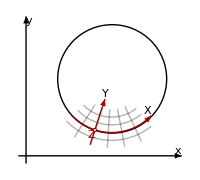

```mathematica
Block[{x,y,X,Y},
With[{p0={1.1,1},r0=0.7,t0=4.4},
With[{ep=p0+r0{Cos[t],Sin[t]}/.t->t0,ep1=p0+(r0+0.2){Cos[t],Sin[t]}/.t->t0,ep2=p0+0.4r0{Cos[t],Sin[t]}/.t->t0},
Show[
Graphics[{
Text[X,p0+r0{Cos[t],Sin[t]}/.t->t0+4.5/4,{1,-1.2}],Text[Y,ep2,{0,-1.3}],
Arrow[{{-0.1,0},{2.,0}}],Arrow[{{0,-0.1},{0,1.8}}],
Text[x,{2,0},{1.2,-2.2}],Text[y,{0,1.8},{-3.5,1.}]}],
ParametricPlot[p0+r{Cos[t],Sin[t]},{r,0.4,r0+0.2},{t,t0-2/4,t0+4/4},Mesh->{4,5},PlotStyle->None,BoundaryStyle->None],
Graphics[{
Circle[p0,r0],Thick,
Darker@Red,Arrow[{ep1,ep2}],
Arrow[Table[p0+r0{Cos[t],Sin[t]},{t,t0-2/4,t0+4.5/4,1/24}]],{EdgeForm@Directive[Thin,Darker@Red],Text[Z,ep,{2.6,1.1}],White,Disk[ep,0.02]}}],
ImageSize->200
]
]]]
```

Figure FigureNumbered.  The coordinate system (X,Y) in a neighborhood of a cycle.

The linearization in Y of the differential equation (EquationNumbered) leads to a homogeneous first-order linear equation:

dY/dX=f(X,0)+(∂f)/(∂Y)(X,0) Y =P(X) Y,

where P(X)=(∂f)/(∂Y)(X,0) is periodic since f is.  So the study of limit cycles naturally leads to the study of linear differential equations with periodic coefficients.

#### Periodic coefficients

Let the homogeneous linear differential equation

dY/dX=P(X) Y

have a periodic coefficient P(X) with period T.  A  solution Y=s(X) with initial condition has values Y_0=s(0) maps to a value Y_1=s(T) after one period.  We can define a mapping A:ℝ→ℝ, called the monodromy operator, by A Y_0=Y_1.

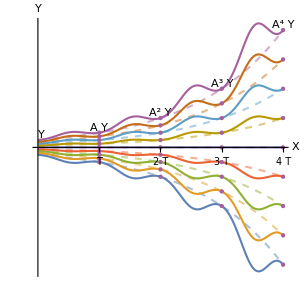

```mathematica
Block[{a,x,y,y0,epilog,X,Y,T},With[{a0=a/.With[{sol0=ParametricNDSolveValue[{y'[x]==(3/5+Sin[x])y[x]/a,y[0]==y0},y,{x,0,8.01Pi},{a,y0}]},
FindRoot[sol0[a,1.][6Pi]==sol0[a,0.5][8Pi],{a,4,4.1}]
],
b0=0.75},
Show[
With[{sol=ParametricNDSolveValue[{y'[x]==(3/5)y[x]/a0,y[0]==y0},y,{x,-0.01,8.01Pi},{y0}]},
Plot[Evaluate@Table[sol[b0 b][x],{b,-1.,1.,1/4}],
{x,0,8.001Pi},
PlotStyle->{{Dashed,Opacity[0.5]}},
Mesh->{{0,2Pi,4Pi,6Pi,8Pi}},AxesOrigin->{0,0},AspectRatio->Automatic,ImageSize->300,GridLines->{2Pi Range[4],Join[
Table[sol[b0][2Pi x],{x,0,4}],Table[sol[-b0][2Pi x],{x,0,4}]]}]
],
With[{sol=ParametricNDSolveValue[{y'[x]==(3/5+Sin[x])y[x]/a0,y[0]==y0},y,{x,-0.01,8.01Pi},{y0}]},
epilog=Table[Text[A^n Y,{2n Pi,sol[b0][2n Pi]},{{-1.,0.,0.2,0.45,0.4}[[1+n]],-1.2}],{n,0,4}];
Plot[Evaluate@Table[sol[b0 b][x],{b,-1.,1.,1/4}],
{x,0,8.001Pi},
Mesh->{{0,2Pi,4Pi,6Pi,8Pi}}]
],
Graphics[epilog],
PlotRange->All,Ticks->{Table[{2 n Pi,n T},{n,4}],None},
AxesLabel->{X,Y},PlotRangePadding->{Automatic,{Automatic,Scaled[0.04]}}
]]
]
```

Figure FigureNumbered.  The monodromy operator A acts by scaling Y (in this image by λ>1).

Theorem.  The monodromy operator of equation (EquationNumbered) is linear and given by A(Y)=λ Y for a positive number λ.  If the multiplierλ>1, then all nontrivial solutions approach infinity as X→+∞; if λ<1, then all solutions approach 0; and if λ=1, then all solutions are bounded.

Note:  Recall that s(X+T) corresponds to translation by -T of s(X).

Proof:  It is easy to see from equation (EquationNumbered) that the multiplier is given by

log λ =∫_x_0^(x_0+T) P(t) dt = ∫_0^T P(t) dt

by the periodicity of P and is the same for all solutions.  Equivalently from the facts (i) that dilation along the Y axis transforms integral curves into integral curves and (ii) that translation along the X axis by -T also transforms integral curves into integral curves by the periodicity of P, it follows that the translation corresponds to scaling by a certain factor.

In other words, s(X+T)=λ s(X). By induction we have that for any positive integer n, s(X+n T)=λ^n s(X).  Hence as n→∞, s(X+n T) approaches ±∞, s(X), 0 according as λ is greater than, equal to, or less than 1.   It follows that solutions tend to infinity, are bounded, or vanish as x→+∞. ■

Remark:  The symmetry of the extended phase space of can be seen in Fig. (FigureNumbered), in which the gray vertical lines illustrate translation by ±n T and the horizontal lines show dilation by λ.  This symmetry is essentially the content of the theorem.  The symmetry looks like a the product of the continuous group of dilations of a homogeneous linear differential equation and a discrete group of translations due to the periodicity of the coefficient.  What the theorem above shows is that a translation is not a new, independent symmetry but corresponds to a dilation, which follows in part from the uniqueness of solutions:  If the solution s_0 with initial condition (0,Y_0) is transformed by translation by T into the solution s_1 with initial condition (T,Y_0), since s_1(X)=s_0(X-T)  implies s_1(T)=s_0(0)=Y_0.  At X=0, the solutions_1(0)=s_0(-T)=λ^-1 y_0.By the uniqueness of solutions, s_1 is the solution with initial condition (0, λ^-1 Y_0), which corresponds to the integral curve obtained by dilation of s_0 by λ^-1.

An extreme example is also the simplest, the exponential function: dy/dx=y.  The coefficient P(x)=1 is periodic of period T for every positive real number T.  Translation by -T corresponds to dilation by λ=e^T: e^(x+T)=e^T e^x.

#### Limit cycles again

Let us return to the linearization (EquationNumbered) of the system with a limit cycle.  The behavior of the phase curves near the cycle can now be determined from the linearization.  If the multiplier λ<1, the limit cycle will be stable, that is nearby integral curves approach the cycle.  If λ>1, then the cycle will be unstable.  If λ=0, then the higher order perturbations of f(X,Y) in equation (EquationNumbered) will determine the stability.

One might wonder if there is a connection between the multiplier and the derivative of the Poincaré map Φ of the original system (EquationNumbered), since in both cases the number 1 is the boundary between stable and unstable cycles.  First, notice that in this context of a cycle, the Poincaré return map of the linearization is the same as the monodromy operator A, since the curve that starts at Y=s(0) returns to A Y=s(T).Next, it turns out one can show that the linearization of Φ  about Y=0 coincides with the monodromy operator, and it follows that Φ'(0)=λ.

Example

Let us study the limit cycle at r=2 of the system given in polar coordinates by

ṙ | = | r (2-r)(x-1)=r (2-r)(r cos θ-1)
θ̇ | = | 1

We pick new coordinates X,Y such that X=θ and the cycle corresponds to Y=r-2=0.  The system becomes

Ẏ | = | (Y+2) (-Y)((Y+2) cos θ-1)
Ẋ | = | 1

Writing dY/dX=Ẏ/OverDot[X,] we obtain the equation

dY/dX  =  (Y+2) (-Y)((Y+2) cos θ-1)

dY/dX | = | (Y+2) (-Y)((Y+2) cos θ-1)
  | = | (2-4 cos X) Y+(1-4 cos X) Y^2 -(cos X)Y^3

Calling the right-hand side f(X,Y), the linearization is given by

(∂f)/(∂Y)(X,0) Y=(2-4 cos X)Y

The linearized differential equation is therefore

dY/dX=(2-4 cos X)Y

The multiplier λ may be found with the follow integral

log λ  = ∫_0^(2π) (2-4 cos X) dX=4π, or λ = exp(4π).

Since λ>1, the cycle is unstable.

```mathematica
sp=With[{scale=1},Show[
StreamPlot[{1,r(2-r)(r Cos[θ]-1)/3}/.r->scale*r,{θ,0,2Pi},{r,0.5/scale,3.9/scale},
StreamPoints->{{{{0.01,2/scale},Red},Automatic}}]
]
];
polarbackground=PolarPlot[0,{t,0,2Pi},
PolarAxes->True,PolarAxesOrigin->{0,3.9},PolarTicks->{"Radians", Automatic},PolarGridLines->Automatic];

Show[
polarbackground,
sp/.Arrow[p_]:>Arrow[Function[{th,r},{r Cos[th],r Sin[th]}]@@@p]]
```

-Graphics-

Figure FigureNumbered.  The phase portrait of  ṙ= (2-r)(x-1), with the limit cycle at r=2 highlighted.

Exercises

Apply the method for finding an integrating factor that is a function of x alone to find an integrating factor of the linear equation (P(x) y+Q(x)) dx+dy=0.

Apply the method for finding an integrating factor that is a function of y alone to find an integrating factor of the linear equation dx+(P(y) x+Q(y)) dy=0.

Show that the substitution y→y/k transforms the homogeneous linear equation (EquationNumbered) into itself.  This also shows that the integral curves of (EquationNumbered) are transformed into themselves by the group of dilations.

Show that the substitution z=y^(1-n) transforms the equation y′+P(x) y=Q(x) y^n into a linear equation.  This equation is called a Bernoulli equation.

Show that if y=f(x) is a nontrivial solution to dy/dx+P(x) y=0, then f(x)≠0 for all x in the domain of f.

Show that the substitution u=x^2 transforms the differential equation dy/dx+2x y=0 into a homogeneous linear equation with constant coefficients.  For a positive real number T, let the mapping ϕ=ϕ_T:x↦√(x^2+T) act on an integral curve y=s(x) by transforming it to y=s(ϕ_T(x))=s(√(x^2+T)):

(a) Show that the mapping ϕ transforms an integral curve into another integral.  (Hint: Find the general solution s and consider s(√(x^2+T)).)
(b) Show that the transformation by ϕ corresponds to a dilation along the y axis and find the multiplier.
(c) Show that the transformation of an integral curve twice by ϕ_T is equivalent to a transformation by ϕ_(2T).

Show that the substitution u=x^2 transforms the differential equation dy/dx+(2x cos x^2) y=0 into a homogeneous linear equation with periodic coefficients of period T=2π.  As in the previous problem, let the mapping ϕ=ϕ_T:x↦√(x^2+2π) act on an integral curve y=s(x):

(a) Show that the mapping ϕ transforms an integral curve into another integral.
(b) Show that the transformation by ϕ corresponds to a dilation along the y axis and find the multiplier.

Show that in a homogeneous linear differential equation with periodic coefficients dy/dx+P(x) y=0, the zero solution is an equilibrium position that is stable if the multiplier λ<1 and unstable if λ>1.

Determine the stability of the limit cycle r=1 of the system given in polar coordinates by
	ṙ=(r^2-1)(2y-1), θ^,=1.
(Hint: If you use the local coordinates X=θ, Y=r-1, then convert the y to polar, substitute r=Y+1, and linearize about Y=0:
	dY/dX=f(X,0)+(∂f)/(∂Y)(X,0) Y.)

Determine the stability of the limit cycle r=1 of the system given in polar coordinates by
	ṙ=(r^2-r)(2x+1), θ^,=1.